0.0002

2.×10^-7

45 °

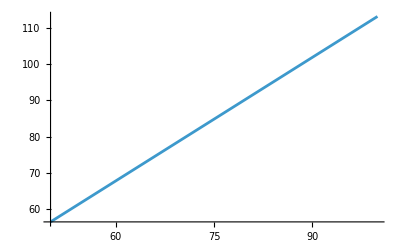

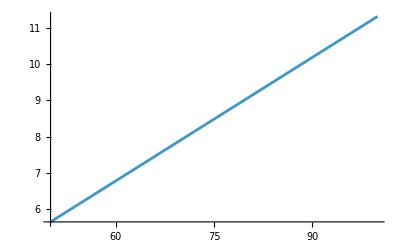

```mathematica
ClearAll["Global`*"]
m=0.2*10^-3
S=0.2*10^-6
alfa=45*Degree
(*zmiana pędu*)
vk[v_]:=0.6*v
p1[v_]:=-m*v*Cos[alfa]
p2[v_]:=m*vk[v]*Cos[alfa]
dp[v_]:=p2[v]-p1[v]
F[v_,dt_]:=dp[v]/dt
P[v_,dt_]:=F[v,dt]/S
(**)
Plot[P[v,0.001]*10^-6,{v,50,100}]
Plot[P[v,0.01]*10^-6,{v,50,100}]
```